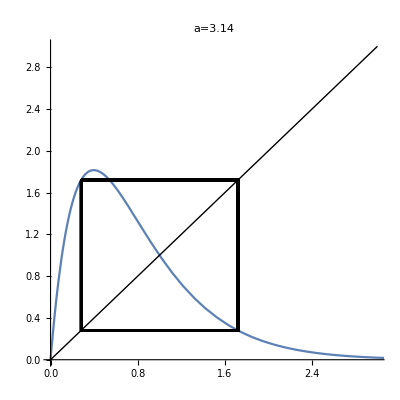

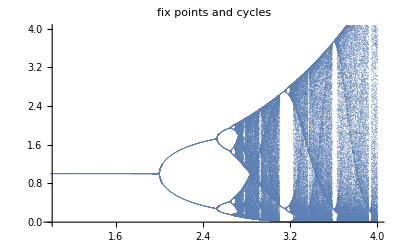

```mathematica
Clear["`*"]; 
a =. ;
g[x_]:=x*Exp[(a*(1-x))];
(*solg1=Solve[x==g[x],x];
solg2=Solve[x==g[g[x]],x];*)
 a = 2.52;start = 1.73;iter = 500;
(*xfp=x /.solg1[[2]];
x2c1=x /.solg2[[3]];
x2c2=x /.solg2[[4]];*)

points=NestList[g,start,iter-1];
lines[x_]:=Line[{{x,x},{x,g[x]},{g[x],g[x]}}];
listlines=lines /@ points;
Plot[g[x], {x,0,5.0},
AspectRatio->Automatic,
PlotLabel->"a=3.14",
PlotRange->{{0,3.0},{0,3.0}},
Epilog->{Line[{{0,0},{3.0,3.0}}],listlines}]

nstart=500;number=128;

afixpoint:=
Union[
Map[
{a,#}&,
NestList[g,Nest[g,start,nstart],number-1]
]
];
amin =1.0;amax=4.0;step=0.001;
fixpoints=Flatten[Table[afixpoint,{a,amin,amax,step}],1];
ListPlot[fixpoints,
PlotLabel->"fix points and cycles",
PlotRange->{{1.0,4.0},{0.0,4.0}},
PlotStyle->PointSize[0.001]]
```